## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="TPI";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_TPI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{dhap,Null,Keq substrate}

{0.107,Keq value}

{g3p,Km or S05 substrate}

{0.00103,Km or S05 value}

{{{g3p,Null}},kcat substrates}

{9000,kcat value}

{2-phosphoglycolate,Inhibition or activation constant substrate}

{0.006,Inhibition or activation constant value}

(dhap^c⇌g3p^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | dhap,Null | 0.107 | 0.10165
0.11235 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9000 | 8833
9167 | 1/s | 7.6 | 25 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities =Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(dhap^c⇌g3p^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | dhap,Null | 0.107 | 0.10165
0.11235 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9000 | 8833
9167 | 1/s | 7.6 | 25 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### mechanism

```mathematica
catalyticBranch={"E_TPI[c] + dhap[c] <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c] + g3p[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TPI^c)_^+dhap^c⇌(TPI^c&dhap^c)_^)^TPI1,((TPI^c&g3p^c)_^⇌(TPI^c)_^+g3p^c)^TPI2,((TPI^c&dhap^c)_^⇌(TPI^c&g3p^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{dhap^c→0}

{g3p^c→0}

{dhap^c→∞}

{g3p^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
TPIRateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",TPIRateConsts, "MX"]
```

{k_TPI1^⟵,k_TPI1^⟶,k_TPI2^⟵,k_TPI2^⟶,k_TPI3^⟵,k_TPI3^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/TPI_rateConsts.m

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/haldaneRatio_1.txt"	0.107
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/relRateRev_g3p.txt"	0.9090909090909091
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000
1	0	0.01	1	7.6	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/TPI/fit_TPI/input/absRateRev.txt"	9000

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=50;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.904492983672
best_fit: 0.954799744317
best_fit: 0.890639235358
best_fit: 0.698166981526
best_fit: 1.02885313565
best_fit: 0.964709604317
best_fit: 1.09754411558
best_fit: 0.796337844017
best_fit: 0.86794415185
best_fit: 1.06296566191
best_fit: 0.859057409372
best_fit: 0.50449066109
best_fit: 0.367102959892
best_fit: 0.68120443321
best_fit: 0.387561761578
best_fit: 0.753991205128
best_fit: 0.422993553981
best_fit: 0.90572003663
best_fit: 0.463900468824
best_fit: 0.919488456909
best_fit: 0.749406560473
best_fit: 0.73982115419
best_fit: 0.882380745879
best_fit: 0.550142605786
best_fit: 0.947247143235
best_fit: 1.02953444413
best_fit: 0.426756407042
best_fit: 0.796503597023
best_fit: 1.09628369511
best_fit: 1.06674700871
best_fit: 0.835609880847
best_fit: 0.615502209217
best_fit: 1.09596172664
best_fit: 0.765229364115
best_fit: 0.65830411949
best_fit: 0.992020706327
best_fit: 0.540395153499
best_fit: 1.09024778674
best_fit: 1.04165353633
best_fit: 1.03089370855
best_fit: 0.218714968623
best_fit: 0.747016417696
best_fit: 0.968035402107
best_fit: 0.255512397338
best_fit: 0.82036834247
best_fit: 0.203408626004
best_fit: 0.892394667153
best_fit: 0.58226206153
best_fit: 0.708836636651
best_fit: 0.39640288036

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | haldaneRatio_1 | 5.20928×10^-12 | 2.71366×10^-23 | 1.28345×10^-12 | 1.19948×10^-9 | 0.107 | 0.107
1 | relRateRev_g3p | 4.40159×10^-12 | 1.9374×10^-23 | 9.21374×10^-13 | 1.01351×10^-9 | 0.0909091 | 0.0909091
1 | relRateRev_g3p | 4.17932×10^-12 | 1.74667×10^-23 | 1.31656×10^-12 | 9.62348×10^-10 | 0.136807 | 0.136807
1 | relRateRev_g3p | 3.86968×10^-12 | 1.49744×10^-23 | 1.78885×10^-12 | 8.91037×10^-10 | 0.20076 | 0.20076
1 | relRateRev_g3p | 3.46312×10^-12 | 1.19932×10^-23 | 2.27063×10^-12 | 7.97419×10^-10 | 0.284747 | 0.284747
1 | relRateRev_g3p | 2.96863×10^-12 | 8.81274×10^-24 | 2.64444×10^-12 | 6.8356×10^-10 | 0.386863 | 0.386863
1 | relRateRev_g3p | 2.4209×10^-12 | 5.86074×10^-24 | 2.7871×10^-12 | 5.57421×10^-10 | 0.5 | 0.5
1 | relRateRev_g3p | 1.87311×10^-12 | 3.50855×10^-24 | 2.64444×10^-12 | 4.31297×10^-10 | 0.613137 | 0.613137
1 | relRateRev_g3p | 1.3787×10^-12 | 1.90082×10^-24 | 2.27063×10^-12 | 3.17458×10^-10 | 0.715253 | 0.715253
1 | relRateRev_g3p | 9.71986×10^-13 | 9.44758×10^-25 | 1.78879×10^-12 | 2.23812×10^-10 | 0.79924 | 0.79924
1 | relRateRev_g3p | 6.62373×10^-13 | 4.38738×10^-25 | 1.3165×10^-12 | 1.52515×10^-10 | 0.863193 | 0.863193
1 | relRateRev_g3p | 4.40162×10^-13 | 1.93742×10^-25 | 9.21374×10^-13 | 1.01351×10^-10 | 0.909091 | 0.909091
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.
1 | absRateRev | 1.15374×10^-12 | 1.33112×10^-24 | 2.39197×10^-8 | 2.65775×10^-10 | 9000 | 9000.

### Simulated Data and Best Fit Data Plot

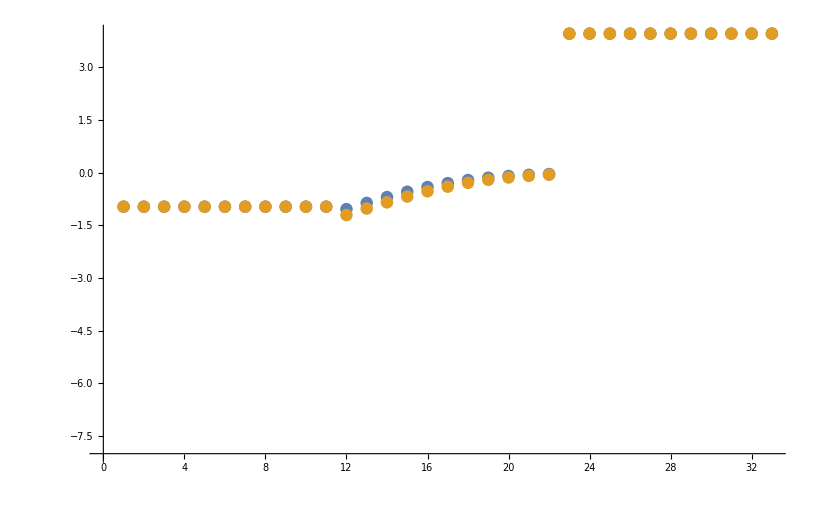

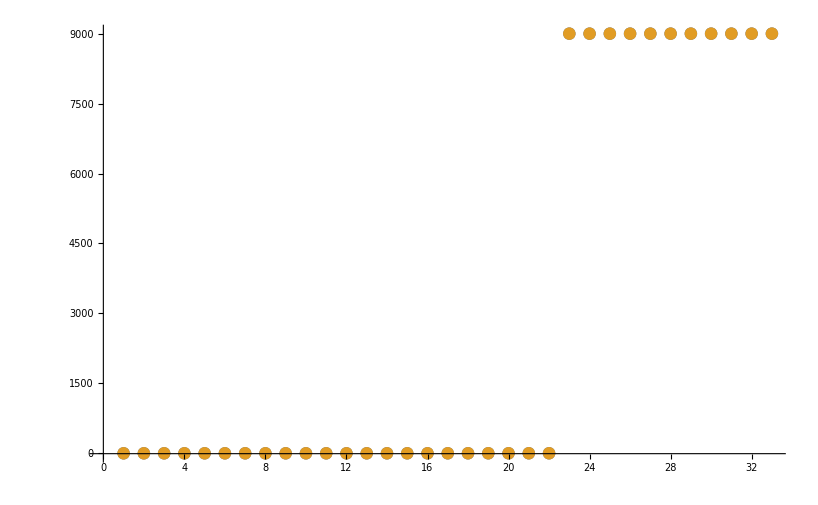

```mathematica
datasetI=20;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

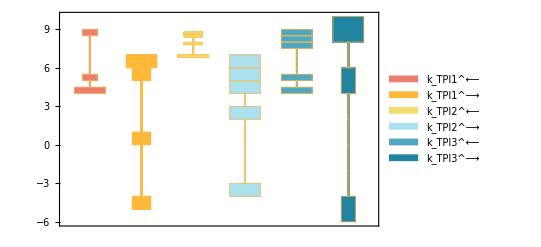

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

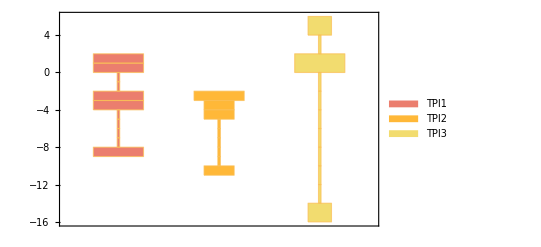

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

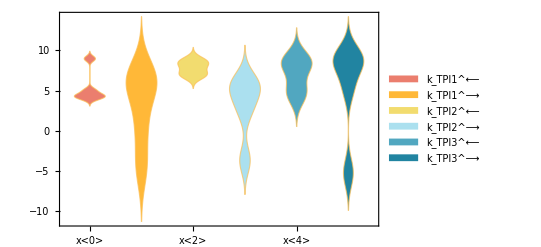

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

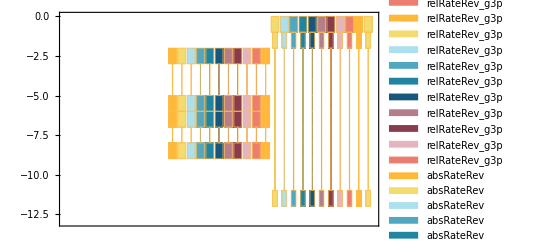

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 5;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00103 | 0.000502615 | 51.2024

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
9000 | 8999.99 | 0.000126519

```mathematica
backCalculateRatios[haldaneDataList[[1]][[1]], haldaneDataList[[1]][[2]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
0.107411 | 0.107412 | 0.000953614